# Calculation of eikonal corrections at KE = 10 MeV

9/23/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.01(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp10a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp10a.csv"];
pp10b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp10b.csv"];
```

```mathematica
(*pp10a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp10a.csv"];
pp10b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp10b.csv"];*)
```

```mathematica
pp10a=Transpose[{pp10a[[All,1]],pp10a[[All,2]]+I*pp10a[[All,3]]}];
pp10b=Transpose[{pp10b[[All,1]],pp10b[[All,2]]+I*pp10b[[All,3]]}];
```

```mathematica
θpp10=Transpose[{pp10a[[All,1]],(pp10a[[All,2]]+pp10b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp10=θtoq/@θpp10;
```

```mathematica
pn10a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn10a.csv"];
pn10b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn10b.csv"];
```

```mathematica
(*pn10a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn10a.csv"];
pn10b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn10b.csv"];*)
```

```mathematica
pn10a=Transpose[{pn10a[[All,1]],pn10a[[All,2]]+I*pn10a[[All,3]]}];
pn10b=Transpose[{pn10b[[All,1]],pn10b[[All,2]]+I*pn10b[[All,3]]}];
```

```mathematica
θpn10=Transpose[{pn10a[[All,1]],(pn10a[[All,2]]+pn10b[[All,2]])/2}];
```

```mathematica
pn10=θtoq/@θpn10;
```

```mathematica
NN10=(pp10+pn10)/2;
f=Interpolation[NN10];
fp=Interpolation[pp10];
fn=Interpolation[pn10];
```

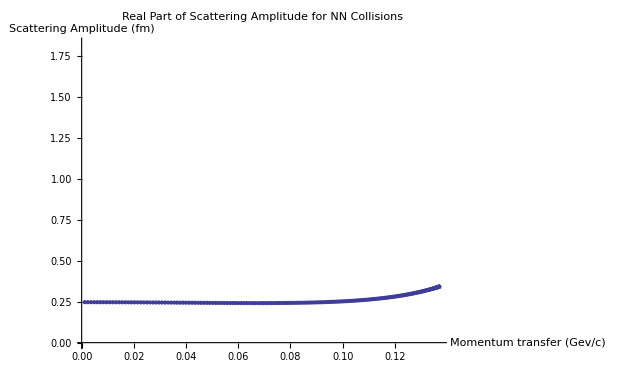

```mathematica
ListPlot[Transpose[{NN10[[All,1]],Re[NN10[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1.82}]
```

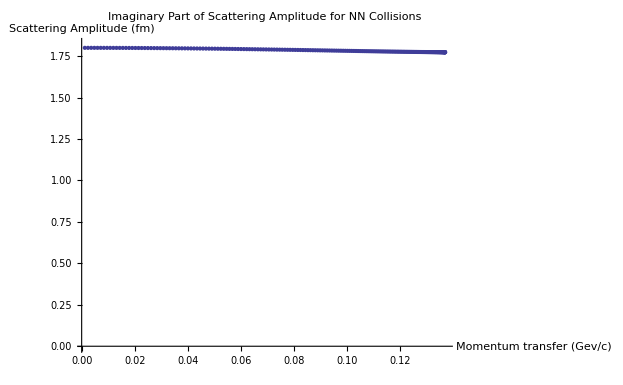

```mathematica
ListPlot[Transpose[{NN10[[All,1]],Im[NN10[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1.82}]
```

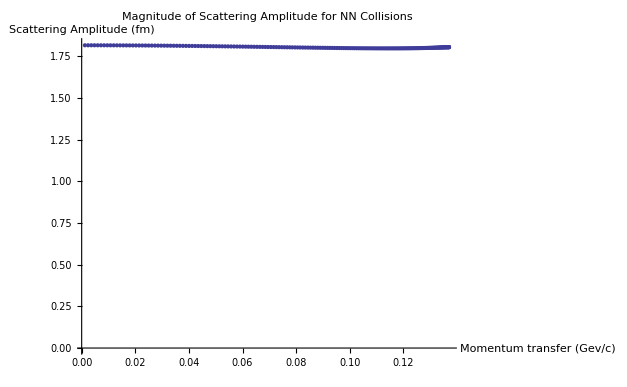

```mathematica
ListPlot[Transpose[{NN10[[All,1]],Abs[NN10[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1.82}]
```

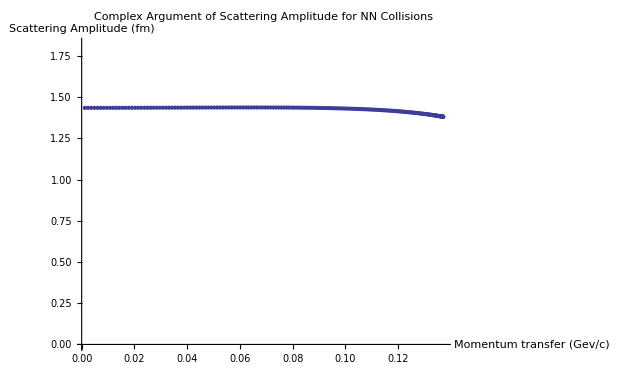

```mathematica
ListPlot[Transpose[{NN10[[All,1]],Arg[NN10[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1.82}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→1.81684,βre→1.2465}

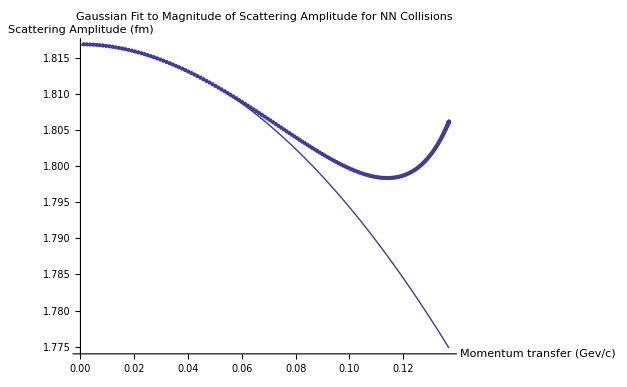

```mathematica
Npts=50;
FindFit[Transpose[{NN10[[1;;Npts,1]],Abs[NN10[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN10[[All,1]],Abs[NN10[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

{ρ→0.136868,βim→-0.737201}

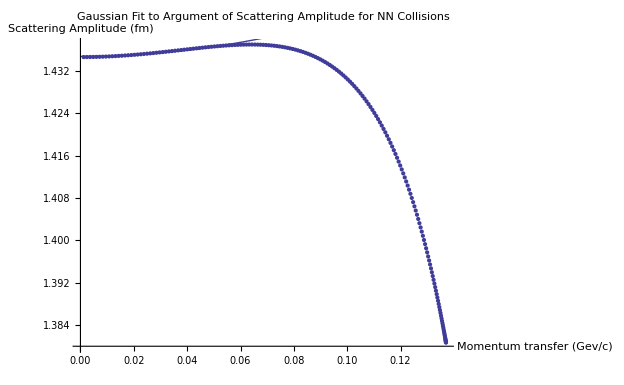

```mathematica
FindFit[Transpose[{NN10[[1;;Npts,1]],Arg[NN10[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN10[[All,1]],Arg[NN10[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==1.8168386375352996&&ρ==0.13686833674011162,{σ,ρ}]
```

{{σ→65.1454,ρ→0.136868}}

Fitted parameters:

```mathematica
σ=65.14536529949699;
ρ=0.13686833674011162;
β=1.2465033945953365-0.7372012410057254 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-42.7682-17.9844 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

-5497.15

```mathematica
ρ0[q_]:=Exp[-B q^2]
```

InterpolatingFunction::dmval: Input value {0.000619367} lies outside the range of data in the interpolating function. Extrapolation will be used.

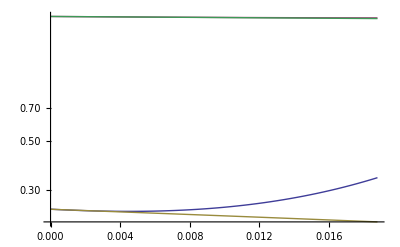

```mathematica
LogPlot[{Re[f[Sqrt[q]]],Im[f[Sqrt[q]]],Re[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]],Im[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]]},{q,0,(2 κ)^2}]
```

InterpolatingFunction::dmval: Input value {0.000619367} lies outside the range of data in the interpolating function. Extrapolation will be used.

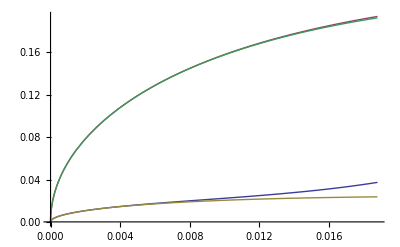

```mathematica
Plot[{Re[Sqrt[q]f[Sqrt[q]] ρ0[Sqrt[q]]],Im[Sqrt[q] f[Sqrt[q]] ρ0[Sqrt[q]]],Re[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]],Im[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]]},{q,0,(2 κ)^2}]
```

```mathematica
Γp=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fp[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
Γn=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fn[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
```

```mathematica
Γ[b_]=(Γp[b]+Γn[b])/2;
```

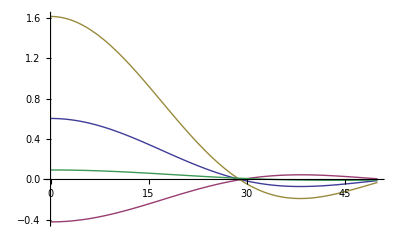

```mathematica
Plot[{Re[Γp[b]],Im[Γp[b]],Re[Γn[b]],Im[Γn[b]]},{b,0,50},PlotRange->All]
```

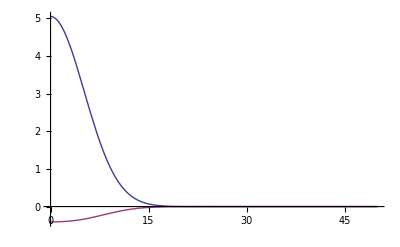

```mathematica
Plot[{Re[σ/ℏc^2 (1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))],Im[σ /ℏc^2(1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))]},{b,0,50},PlotRange->All]
```

```mathematica
Γ[0]
```

1.10966-0.162891 ⅈ

```mathematica
Table[{q,I κ ℏc Exp[q^2B/A] NIntegrate[BesselJ[0,b q](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]},{q,0,2 k,.01}]
```

{{0.,-0.00643491+0.214814 ⅈ},{0.01,-0.00567061+0.217623 ⅈ},{0.02,-0.0034686+0.225571 ⅈ},{0.03,-0.0000894179+0.23729 ⅈ},{0.04,0.00407129+0.250726 ⅈ},{0.05,0.00853483+0.263434 ⅈ},{0.06,0.0128016+0.27294 ⅈ},{0.07,0.0164147+0.277091 ⅈ},{0.08,0.019016+0.274363 ⅈ},{0.09,0.0203872+0.264068 ⅈ},{0.1,0.0204713+0.246443 ⅈ},{0.11,0.0193706+0.222602 ⅈ},{0.12,0.0173247+0.194371 ⅈ},{0.13,0.0146708+0.164024 ⅈ},{0.14,0.0117929+0.13398 ⅈ},{0.15,0.00906879+0.106483 ⅈ},{0.16,0.00682081+0.0833389 ⅈ},{0.17,0.00527805+0.0657182 ⅈ},{0.18,0.00455435+0.0540708 ⅈ},{0.19,0.00464389+0.0481419 ⅈ},{0.2,0.0054338+0.0470856 ⅈ},{0.21,0.00673057+0.0496493 ⅈ}}

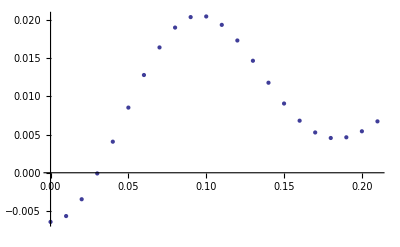

```mathematica
ListPlot[Re[%]]
```

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

-5497.15

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γ[b])^A),{b,0,50}]]
```

-200.018

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]]
```

-169.669